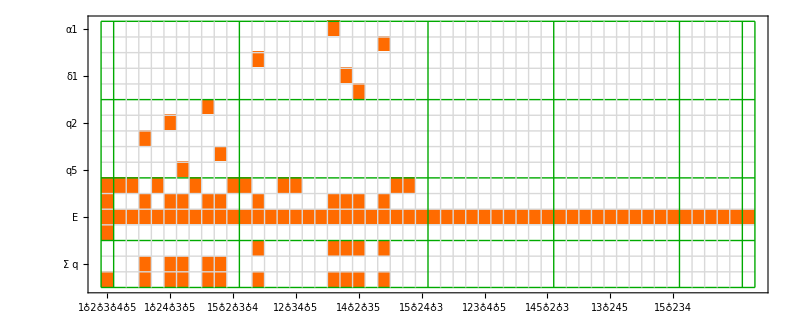
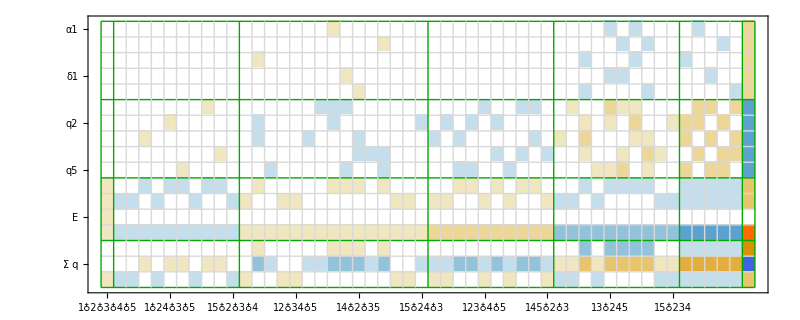
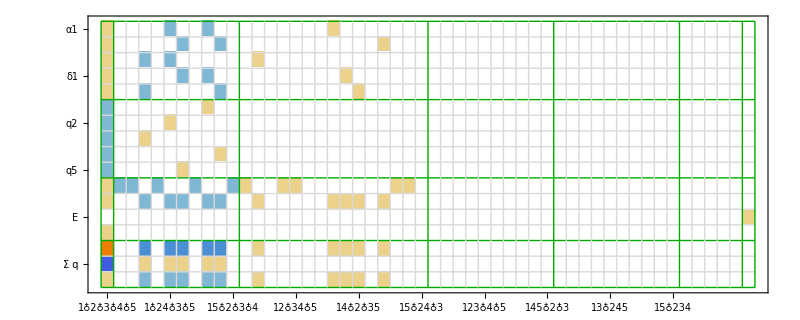
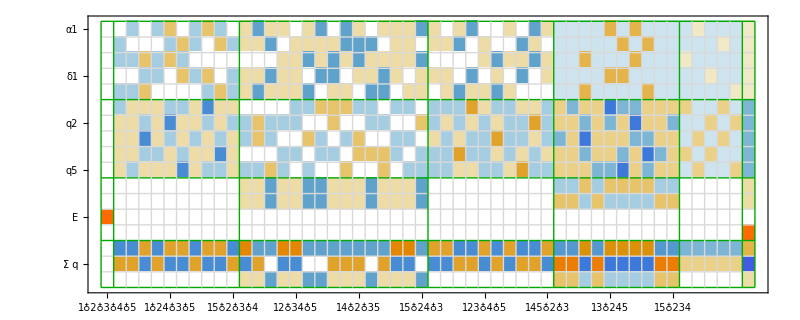
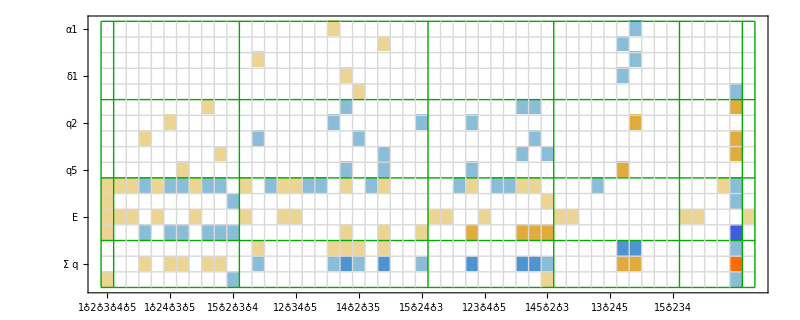
{-Graphics-C,-Graphics-E,-Graphics-G,-Graphics-F,-Graphics-T}

```mathematica
Table[
Labeled[
MatrixPlot[
Append[
Append[
Append[
Table[
BaseCoeff[k,base],{k,
Join[
alfa1s,
quads,
{starKey,lambdaKey,0,K5Key}
]}],
Total[Table[
BaseCoeff[k,base],{k,
alfa1s}]]
],
Total[Table[
BaseCoeff[k,base],{k,
quads}]]
],
Total[Table[
BaseCoeff[k,base],{k,
Join[
alfa1s,
quads,
{K5Key}
]}]]
],Mesh->{{{0,Directive[Darker[Green],Thick]},1,2,3,4,{5,Directive[Darker[Green],Thick]},6,7,8,9,{10,Directive[Darker[Green],Thick]},11,12,13,{14,Directive[Darker[Green],Thick]},15,16,{17,Directive[Darker[Green],Thick]}},MyMesh[base]},MeshStyle->LightGray,Frame->True,FrameTicks->{{{1,"α1"},{2,"β1"},{3,"γ1"},{4,"δ1"},{5,"ϵ1"},{6,"q1"},{7,"q2"},{8,"q3"},{9,"q4"},{10,"q5"},{11,"star"},{12,"λ"},{13,"E"},{14,"K5"},{15,"Σ α"},{16,"Σ q"},{17,"Σ αqK5"}},MyTicks[base]},ImageSize->800
],base],{base,allBases}
]
```